```mathematica
SetDirectory["D:\\program files\\Wolfram Research\\Mathematica\\7.0\\AddOns\\ExtraPackages\\MadEvent analysis\\parameter_scans\\plots_for_pub"];
Timing[testp=Import["ax_shower.lhe","Table"];]
```

{5.77204,Null}

```mathematica
Timing[testp2=Import["grv_shower.lhe","Table"];]
```

{5.99044,Null}

```mathematica
Timing[testp3=Import["rpv_shower.lhe","Table"];]
```

{5.58484,Null}

```mathematica
Timing[eventListp=ReadME[testp]; ]
```

{0.2652,Null}

```mathematica
ClearSystemCache[];Timing[eventListp=ReadME[testp];]
```

{0.2652,Null}

```mathematica
Timing[eventListp2=ReadME[testp2]; ]
```

{0.2808,Null}

```mathematica
Timing[eventListp3=ReadME[testp3];]
```

{0.2652,Null}

```mathematica
Nev = Length[eventListp]-1
```

10000

```mathematica
Nev2 = Length[eventListp2]-1
```

10000

```mathematica
Nev3= Length[eventListp3]-1
```

10000

```mathematica
tsp={eventListp[[1]],eventListp2[[1]]};
EventPrint /@ %;
```

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
uBar | in | 0 | 0 | 0 | 0 | 0.108 | 0.525 | 237. | 237. | 0. | 0 | 0
u | in | 0 | 0 | 0 | 0 | 121. | -132. | -2900. | 2910. | 0. | 0 | 0
(χ̃)_0 | decayed | 1 | 1 | 0 | 0 | -651. | 250. | -801. | 1080. | 202. | 0 | 0
(χ̃)_0 | decayed | 1 | 1 | 0 | 0 | 772. | -381. | -1860. | 2060. | 202. | 0 | 0
particle[9000006] | decayed | 3 | 3 | 0 | 0 | -47.8 | 8.2 | -5.57 | 48.8 | 0. | 0 | 0
u | decayed | 3 | 3 | 0 | 0 | -44.3 | 46. | -55.9 | 84.9 | 0. | 0 | 0
uBar | decayed | 3 | 3 | 0 | 0 | -559. | 196. | -739. | 947. | 0. | 0 | 0
particle[9000006] | decayed | 4 | 4 | 0 | 0 | 225. | -108. | -637. | 684. | 0. | 0 | 0
u | decayed | 4 | 4 | 0 | 0 | 551. | -250. | -1190. | 1340. | 0. | 0 | 0
uBar | decayed | 4 | 4 | 0 | 0 | -4.01 | -23.5 | -36.2 | 43.3 | 0. | 0 | 0
particle[9000006] | out | 3 | 3 | 0 | 0 | -47.8 | 8.2 | -5.57 | 48.8 | 0. | 0 | 0
particle[9000006] | out | 4 | 4 | 0 | 0 | 225. | -108. | -637. | 684. | 0. | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -597. | 259. | -801. | 1040. | 103. | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 527. | -270. | -1180. | 1320. | 26.9 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -121. | 126. | -549. | 576. | 18.6 | 0 | 0)

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
uBar | in | 0 | 0 | 0 | 0 | 8.68 | -1.42 | 546. | 546. | 0. | 0 | 0
u | in | 0 | 0 | 0 | 0 | 109. | -113. | -646. | 664. | 0. | 0 | 0
(χ̃)_0 | decayed | 1 | 1 | 0 | 0 | -449. | 42.5 | 183. | 527. | 202. | 0 | 0
(χ̃)_0 | decayed | 1 | 1 | 0 | 0 | 567. | -157. | -283. | 683. | 202. | 0 | 0
particle[1000049] | decayed | 3 | 3 | 0 | 0 | -76.1 | 47.1 | 99.7 | 134. | 0. | 0 | 0
s | decayed | 3 | 3 | 0 | 0 | -44.2 | 9.59 | -18.2 | 48.8 | 0. | 0 | 0
sBar | decayed | 3 | 3 | 0 | 0 | -329. | -14.2 | 102. | 345. | 0. | 0 | 0
particle[1000049] | decayed | 4 | 4 | 0 | 0 | 360. | -66.6 | -244. | 440. | 0. | 0 | 0
d | decayed | 4 | 4 | 0 | 0 | 210. | -97.4 | -41.1 | 235. | 0. | 0 | 0
dBar | decayed | 4 | 4 | 0 | 0 | -3.48 | 6.78 | 2.29 | 7.96 | 0. | 0 | 0
particle[1000049] | out | 3 | 3 | 0 | 0 | -76.1 | 47.1 | 99.7 | 134. | 0. | 0 | 0
particle[1000049] | out | 4 | 4 | 0 | 0 | 360. | -66.6 | -244. | 440. | 0. | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -335. | -15.3 | 108. | 354. | 40.1 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 197. | -96.9 | -41.3 | 225. | 23.9 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -109. | 112. | -364. | 397. | 15.5 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -35.6 | 8.35 | -16.5 | 40.2 | 2.24 | 0 | 0)

```mathematica
eventListOutLp=SetOut[eventListp];
```

```mathematica
eventListOutLp2=SetOut[eventListp2];
```

```mathematica
eventListOutLp3=SetOut[eventListp3];
```

```mathematica
tsp={eventListOutLp[[10000]],eventListOutLp3[[8]]};
EventPrint /@ %;
```

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
particle[9000006] | out | 3 | 3 | 0 | 0 | 139. | -314. | -870. | 936. | 0. | 0 | 0
particle[9000006] | out | 4 | 4 | 0 | 0 | -106. | 372. | -162. | 419. | 0. | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 45.2 | -288. | -839. | 891. | 64.1 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -127. | 257. | -101. | 316. | 89.4 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 52.3 | -76.2 | -143. | 171. | 12.5 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -18.8 | 59. | 9.34 | 62.7 | 3.52 | 0 | 0)

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
gluon | out | 0 | 0 | 0 | 0 | 47.8 | -197. | -143. | 249. | 17.6 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -118. | 120. | -421. | 453. | 15.1 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 43.3 | 121. | -361. | 383. | 14.2 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -11.1 | -11.5 | 2.92 | 16.6 | 3.75 | 0 | 0
⋁_e  | out | 0 | 0 | 0 | 0 | 45.1 | -32.5 | 0. | 55.6 | 0. | 0 | 0)

```mathematica
JustTheNeutrinos= {12,_,_,_,_,_,_,_,_,_,_,_,_}  ;
JustTheBs= {5,_,_,_,_,_,_,_,_,_,_,_,_}  ;
JustTheDM={9000006,_,_,_,_,_,_,_,_,_,_,_,_} |{1000049,_,_,_,_,_,_,_,_,_,_,_,_};
RemoveNeutrinos [event_]:=(DeleteCases[event,JustTheNeutrinos,{2}]);
RemoveBs[event_]:=(DeleteCases[event,JustTheBs,{2}]);
RemoveDM[event_]:=(DeleteCases[event,JustTheDM,{2}]);
eventListOutClean=RemoveBs[RemoveNeutrinos[eventListOutLp]];
eventListOutClean2=RemoveBs[RemoveNeutrinos[eventListOutLp2]];
eventListOutClean3=RemoveBs[eventListOutLp3];
eventListOutJets= RemoveDM[eventListOutClean];
eventListOutJets2= RemoveDM[eventListOutClean2];
eventListOutJets3= RemoveNeutrinos[eventListOutClean3];
```

```mathematica
tsp={eventListOutClean[[1]],eventListOutClean3[[24]]};
EventPrint /@ %;
```

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
particle[9000006] | out | 3 | 3 | 0 | 0 | -47.8 | 8.2 | -5.57 | 48.8 | 0. | 0 | 0
particle[9000006] | out | 4 | 4 | 0 | 0 | 225. | -108. | -637. | 684. | 0. | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -597. | 259. | -801. | 1040. | 103. | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 527. | -270. | -1180. | 1320. | 26.9 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -121. | 126. | -549. | 576. | 18.6 | 0 | 0)

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
gluon | out | 0 | 0 | 0 | 0 | 101. | 210. | -338. | 411. | 21.5 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -22.9 | -127. | 61.7 | 144. | 13.4 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 47.1 | -78.2 | 260. | 276. | 18.7 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -23.2 | 23.6 | 5.21 | 33.7 | 3.51 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -6.03 | -28.5 | 114. | 118. | 6.55 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -14. | -16.4 | 540. | 541. | 3.77 | 0 | 0
⋁_e  | out | 0 | 0 | 0 | 0 | -79. | 13.6 | 0. | 80.1 | 0. | 0 | 0)

```mathematica
tsp={eventListOutJets[[8]],eventListOutJets3[[24]]};
EventPrint /@ %;
```

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
gluon | out | 0 | 0 | 0 | 0 | -0.769 | -142. | -133. | 196. | 19.1 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -72.2 | 45. | -654. | 659. | 11.1 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 53.4 | 61. | 63.7 | 103. | 6.01 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 13.9 | 42.6 | 185. | 190. | 11.7 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 33.4 | -22.1 | -76.9 | 87.3 | 10.2 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -12.1 | -9.36 | -24.6 | 29.2 | 3.76 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -2.62 | -9.69 | 12.4 | 16.1 | 1.9 | 0 | 0)

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
gluon | out | 0 | 0 | 0 | 0 | 101. | 210. | -338. | 411. | 21.5 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -22.9 | -127. | 61.7 | 144. | 13.4 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 47.1 | -78.2 | 260. | 276. | 18.7 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -23.2 | 23.6 | 5.21 | 33.7 | 3.51 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -6.03 | -28.5 | 114. | 118. | 6.55 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -14. | -16.4 | 540. | 541. | 3.77 | 0 | 0)

```mathematica
Cuts[event_]:=If[ptOf[event]>40,event];
eventListOutCutJets=Map[Cuts,eventListOutJets,{2}];
eventListOutCutJets=DeleteCases[eventListOutCutJets,Null,2];
eventListOutCutJets2=Map[Cuts,eventListOutJets2,{2}];
eventListOutCutJets2=DeleteCases[eventListOutCutJets2,Null,2];
eventListOutCutJets3=Map[Cuts,eventListOutJets3,{2}];
eventListOutCutJets3=DeleteCases[eventListOutCutJets3,Null,2];

tsp={eventListOutCutJets[[8]],eventListOutCutJets2[[24]]};
EventPrint /@ %;
```

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
gluon | out | 0 | 0 | 0 | 0 | -0.769 | -142. | -133. | 196. | 19.1 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -72.2 | 45. | -654. | 659. | 11.1 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 53.4 | 61. | 63.7 | 103. | 6.01 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 13.9 | 42.6 | 185. | 190. | 11.7 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 33.4 | -22.1 | -76.9 | 87.3 | 10.2 | 0 | 0)

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
gluon | out | 0 | 0 | 0 | 0 | -240. | -144. | -11.7 | 283. | 42.2 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 137. | 182. | -353. | 423. | 53.6 | 0 | 0)

```mathematica
Exactly4Jets={_,_,_,_} ;
Require4Jets[event_]:=(Cases[event,Exactly4Jets,{1}]);
eventList4CutJets= Require4Jets[eventListOutCutJets];
eventList4CutJets2= Require4Jets[eventListOutCutJets2];
eventList4CutJets3= Require4Jets[eventListOutCutJets3];
Jet4Nev = Length[eventList4CutJets]
Jet4Nev2 = Length[eventList4CutJets2]
Jet4Nev3= Length[eventList4CutJets3]
```

2071

1530

2657

```mathematica
Exactly6Jets={_,_,_,_,_,_} ;
Require6Jets[event_]:=(Cases[event,Exactly6Jets,{1}]);
eventList6CutJets= Require6Jets[eventListOutCutJets];
eventList6CutJets2= Require6Jets[eventListOutCutJets2];
eventList6CutJets3= Require6Jets[eventListOutCutJets3];
Jet6Nev = Length[eventList6CutJets]
Jet6Nev2 = Length[eventList6CutJets2]
Jet6Nev3= Length[eventList6CutJets3]
```

95

64

180

```mathematica
tsp={eventList4CutJets[[10]],eventList4CutJets2[[24]]};
EventPrint /@ %;
```

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
gluon | out | 0 | 0 | 0 | 0 | 5.3 | -192. | -283. | 343. | 30.8 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -108. | -113. | -95.4 | 184. | 21. | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 44.6 | 116. | -155. | 199. | 5.26 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 34.6 | 46.9 | -338. | 343. | 7.07 | 0 | 0)

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
gluon | out | 0 | 0 | 0 | 0 | -71. | -119. | 538. | 556. | 22.4 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -50.6 | 62.9 | 52.8 | 97.1 | 11.2 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | 61. | -6.51 | 99.9 | 119. | 18.1 | 0 | 0
gluon | out | 0 | 0 | 0 | 0 | -60.5 | -9.05 | 177. | 187. | 5.38 | 0 | 0)

```mathematica
numJets[event_]:=Length[event];
numJetsPlot = Map[numJets[#] &, eventListOutJets[[1;;Nev]]];
numJetsBGPlot = Map[numJets[#] &, eventListOutJets2[[1;;Nev2]]];
numJetsRPVPlot= Map[numJets[#] &, eventListOutJets3[[1;;Nev3]]];
```

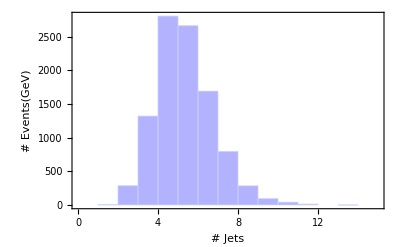

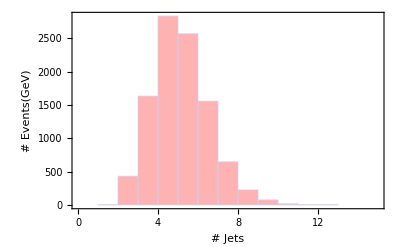

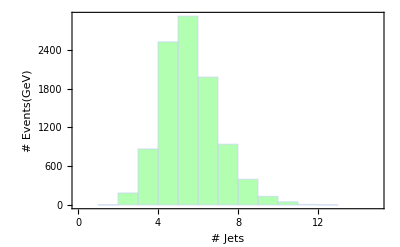

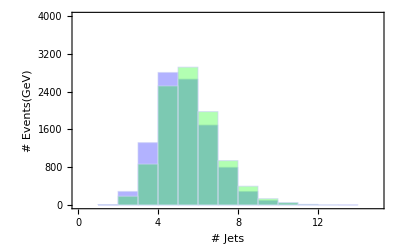

```mathematica
g1=Histogram[numJetsPlot, {0,15,1},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"# Jets","# Events(GeV)"}]
g2=Histogram[numJetsBGPlot, {0,15,1},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"# Jets","# Events(GeV)"}]
g3=Histogram[numJetsRPVPlot, {0,15,1},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"# Jets","# Events(GeV)"}]
Show[g1,g3,PlotRange->{{0,15},{0,4000}}]
```

```mathematica
numJets[event_]:=Length[event];
numJetsPlot = Map[numJets[#] &, eventListOutCutJets[[1;;Nev]]];
numJetsBGPlot = Map[numJets[#] &, eventListOutCutJets2[[1;;Nev2]]];
numJetsRPVPlot= Map[numJets[#] &, eventListOutCutJets3[[1;;Nev3]]];
```

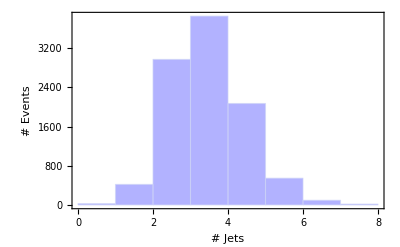

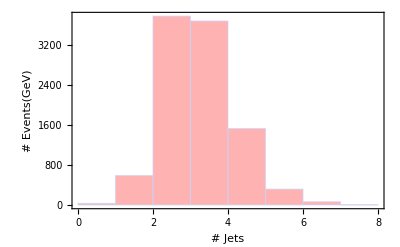

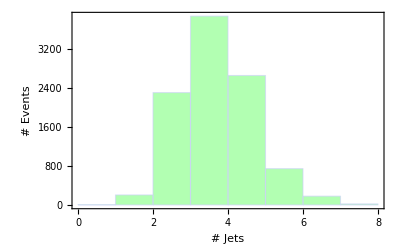

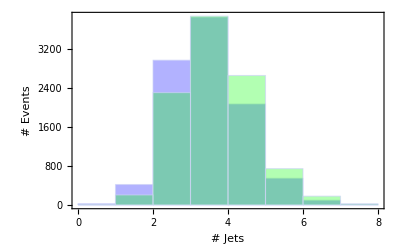

```mathematica
g1=Histogram[numJetsPlot, {0,8,1},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"# Jets","# Events"}]
g2=Histogram[numJetsBGPlot, {0,8,1},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"# Jets","# Events(GeV)"}]
g3=Histogram[numJetsRPVPlot, {0,8,1},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"# Jets","# Events"}]
Show[g1,g3]
```

```mathematica
JetPtTot[event_]:=Total[Map[ptOf[#]&, event],2]
JetPtTotAxPlot = Map[JetPtTot[#] &, eventListOutJets[[1;;Nev]]];
JetPtTotGrvPlot = Map[JetPtTot[#] &, eventListOutJets2[[1;;Nev2]]];
JetPtTotRPVPlot = Map[JetPtTot[#] &, eventListOutJets3[[1;;Nev3]]];
```

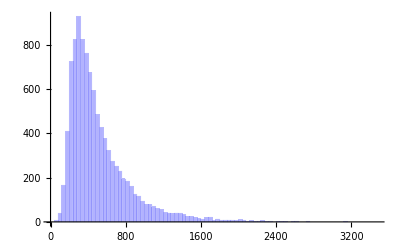

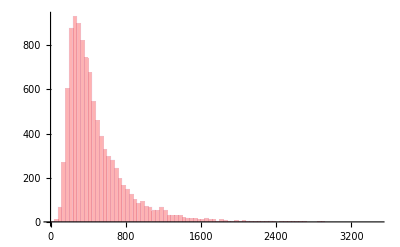

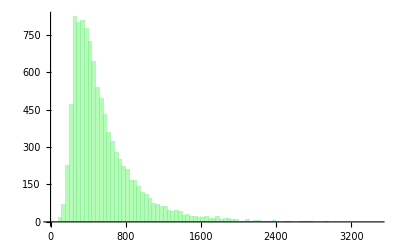

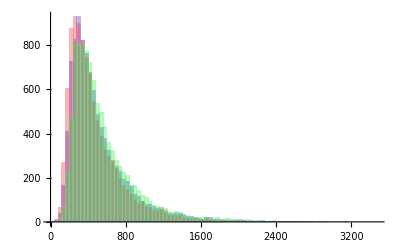

```mathematica
g1=Histogram[JetPtTotAxPlot, {0,3500,40},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=Histogram[JetPtTotGrvPlot, {0,3500,40},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=Histogram[JetPtTotRPVPlot, {0,3500,40},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2,g3]
```

```mathematica
LeadingEta[event_]:=etaOf[First[PTSort[event]]];
LeadingEtaPlot = Map[LeadingEta[#] &, eventListOutJets[[1;;Nev]]];
LeadingEtaBGPlot = Map[LeadingEta[#] &, eventListOutJets2[[1;;Nev2]]];
LeadingEtaRPVPlot = Map[LeadingEta[#] &, eventListOutJets3[[1;;Nev3]]];
```

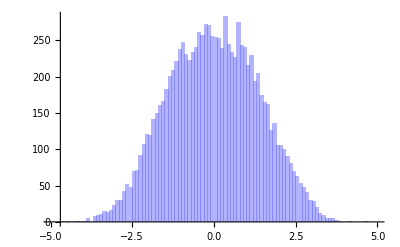

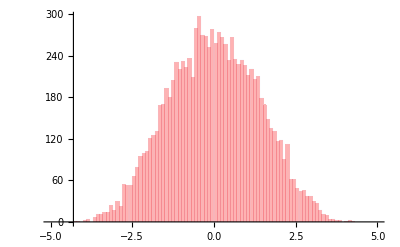

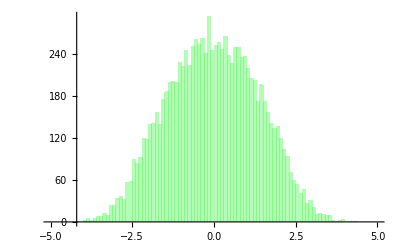

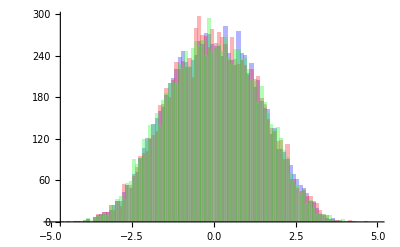

```mathematica
g1=Histogram[LeadingEtaPlot, {-5,5,0.1},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18}]
g2=Histogram[LeadingEtaBGPlot, {-5,5,0.1},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18}]
g3=Histogram[LeadingEtaRPVPlot, {-5,5,0.1},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18}]
Show[g1,g2,g3]
```

```mathematica
InvM1[event_]:=Sqrt[enOf[event[[1]]]*enOf[event[[1]]]-ThreeVectorFrom[event[[1]]].ThreeVectorFrom[event[[1]]]]
InvM2[event_]:=Sqrt[enOf[event[[2]]]*enOf[event[[2]]]-ThreeVectorFrom[event[[2]]].ThreeVectorFrom[event[[2]]]];
InvM3[event_]:=Sqrt[enOf[event[[3]]]*enOf[event[[3]]]-ThreeVectorFrom[event[[3]]].ThreeVectorFrom[event[[3]]]];
InvM4[event_]:=Sqrt[enOf[event[[4]]]*enOf[event[[4]]]-ThreeVectorFrom[event[[4]]].ThreeVectorFrom[event[[4]]]];
InvM12[event_] := Sqrt[2*(enOf[event[[1]]]*enOf[event[[2]]]-ThreeVectorFrom[event[[1]]].ThreeVectorFrom[event[[2]]])];
InvM23[event_] := Sqrt[2*(enOf[event[[3]]]*enOf[event[[2]]]-ThreeVectorFrom[event[[3]]].ThreeVectorFrom[event[[2]]])];
InvM34[event_] := Sqrt[2*(enOf[event[[3]]]*enOf[event[[4]]]-ThreeVectorFrom[event[[3]]].ThreeVectorFrom[event[[4]]])];
InvM41[event_] := Sqrt[2*(enOf[event[[1]]]*enOf[event[[4]]]-ThreeVectorFrom[event[[1]]].ThreeVectorFrom[event[[4]]])];
InvM31[event_] := Sqrt[2*(enOf[event[[3]]]*enOf[event[[1]]]-ThreeVectorFrom[event[[3]]].ThreeVectorFrom[event[[1]]])];
InvM24[event_] := Sqrt[2*(enOf[event[[2]]]*enOf[event[[4]]]-ThreeVectorFrom[event[[2]]].ThreeVectorFrom[event[[4]]])];
InvM51[event_] := Sqrt[2*(enOf[event[[1]]]*enOf[event[[5]]]-ThreeVectorFrom[event[[1]]].ThreeVectorFrom[event[[5]]])];
InvM52[event_] := Sqrt[2*(enOf[event[[2]]]*enOf[event[[5]]]-ThreeVectorFrom[event[[2]]].ThreeVectorFrom[event[[5]]])];
InvM53[event_] := Sqrt[2*(enOf[event[[3]]]*enOf[event[[5]]]-ThreeVectorFrom[event[[3]]].ThreeVectorFrom[event[[5]]])];
InvM54[event_] := Sqrt[2*(enOf[event[[4]]]*enOf[event[[5]]]-ThreeVectorFrom[event[[4]]].ThreeVectorFrom[event[[5]]])];
InvM61[event_] := Sqrt[2*(enOf[event[[1]]]*enOf[event[[6]]]-ThreeVectorFrom[event[[1]]].ThreeVectorFrom[event[[6]]])];
InvM62[event_] := Sqrt[2*(enOf[event[[2]]]*enOf[event[[6]]]-ThreeVectorFrom[event[[2]]].ThreeVectorFrom[event[[6]]])];
InvM63[event_] := Sqrt[2*(enOf[event[[3]]]*enOf[event[[6]]]-ThreeVectorFrom[event[[3]]].ThreeVectorFrom[event[[6]]])];
InvM64[event_] := Sqrt[2*(enOf[event[[4]]]*enOf[event[[6]]]-ThreeVectorFrom[event[[4]]].ThreeVectorFrom[event[[6]]])];
InvM65[event_] := Sqrt[2*(enOf[event[[5]]]*enOf[event[[6]]]-ThreeVectorFrom[event[[5]]].ThreeVectorFrom[event[[6]]])];
InvM123[event_] := Sqrt[(enOf[event[[1]]]+enOf[event[[2]]]+enOf[event[[3]]])*(enOf[event[[1]]]+enOf[event[[2]]]+enOf[event[[3]]])-(ThreeVectorFrom[event[[1]]]+ThreeVectorFrom[event[[2]]]+ThreeVectorFrom[event[[3]]]).(ThreeVectorFrom[event[[1]]]+ThreeVectorFrom[event[[2]]]+ThreeVectorFrom[event[[3]]])];
InvM124[event_] := Sqrt[(enOf[event[[1]]]+enOf[event[[2]]]+enOf[event[[4]]])*(enOf[event[[1]]]+enOf[event[[2]]]+enOf[event[[4]]])-(ThreeVectorFrom[event[[1]]]+ThreeVectorFrom[event[[2]]]+ThreeVectorFrom[event[[4]]]).(ThreeVectorFrom[event[[1]]]+ThreeVectorFrom[event[[2]]]+ThreeVectorFrom[event[[4]]])];
InvM423[event_] := Sqrt[(enOf[event[[4]]]+enOf[event[[2]]]+enOf[event[[3]]])*(enOf[event[[4]]]+enOf[event[[2]]]+enOf[event[[3]]])-(ThreeVectorFrom[event[[4]]]+ThreeVectorFrom[event[[2]]]+ThreeVectorFrom[event[[3]]]).(ThreeVectorFrom[event[[4]]]+ThreeVectorFrom[event[[2]]]+ThreeVectorFrom[event[[3]]])];
InvM143[event_] := Sqrt[(enOf[event[[1]]]+enOf[event[[4]]]+enOf[event[[3]]])*(enOf[event[[1]]]+enOf[event[[4]]]+enOf[event[[3]]])-(ThreeVectorFrom[event[[1]]]+ThreeVectorFrom[event[[4]]]+ThreeVectorFrom[event[[3]]]).(ThreeVectorFrom[event[[1]]]+ThreeVectorFrom[event[[4]]]+ThreeVectorFrom[event[[3]]])];

ResDiffList[event_]:={Abs[InvM12[event]-InvM34[event]],Abs[InvM23[event]-InvM41[event]],Abs[InvM31[event]-InvM24[event]],Abs[InvM123[event]-InvM4[event]],Abs[InvM124[event]-InvM3[event]],Abs[InvM423[event]-InvM1[event]],Abs[InvM143[event]-InvM2[event]]}

ReducedInvMass[event_]:=Which[
Min[ResDiffList[event]]==Abs[InvM12[event]-InvM34[event]],InvM12[event],
Min[ResDiffList[event]]==Abs[InvM23[event]-InvM41[event]],InvM23[event],
Min[ResDiffList[event]]==Abs[InvM31[event]-InvM24[event]],InvM31[event],
Min[ResDiffList[event]]==Abs[InvM123[event]-InvM4[event]],InvM123[event],
Min[ResDiffList[event]]==Abs[InvM124[event]-InvM3[event]],InvM124[event],
Min[ResDiffList[event]]==Abs[InvM423[event]-InvM1[event]],InvM423[event],
Min[ResDiffList[event]]==Abs[InvM143[event]-InvM2[event]],InvM143[event]
];
```

```mathematica
ReduceJetInvMassPlot = Map[ReducedInvMass[#] &, eventList4CutJets[[1;;Jet4Nev]]];
ReducedJetInvMassBGPlot = Map[ReducedInvMass[#] &, eventList4CutJets2[[1;;Jet4Nev2]]];
ReducedJetInvMassRPVPlot = Map[ReducedInvMass[#] &, eventList4CutJets3[[1;;Jet4Nev3]]];
```

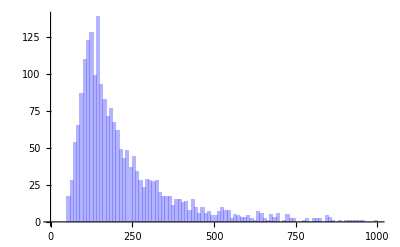

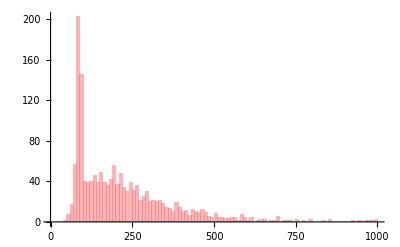

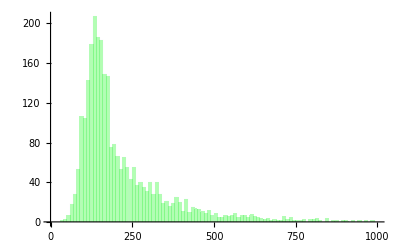

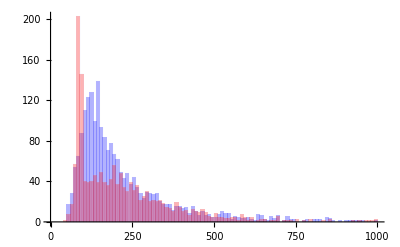

```mathematica
g1=Histogram[ReduceJetInvMassPlot, {0,1000,10},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=Histogram[ReducedJetInvMassBGPlot, {0,1000,10},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=Histogram[ReducedJetInvMassRPVPlot, {0,1000,10},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2]
```

```mathematica
AllInvMassPlot=Flatten[{Map[InvM12[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM23[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM34[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM41[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM31[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM24[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM123[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM124[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM423[#]&,eventList4CutJets[[1;;Jet4Nev]]],Map[InvM143[#]&,eventList4CutJets[[1;;Jet4Nev]]]},1];
AllInvMassBGPlot=Flatten[{Map[InvM12[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM23[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM34[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM41[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM31[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM24[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM123[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM124[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM423[#]&,eventList4CutJets2[[1;;Jet4Nev2]]],Map[InvM143[#]&,eventList4CutJets2[[1;;Jet4Nev2]]]},1];
AllInvMassRPVPlot=Flatten[{Map[InvM12[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM23[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM34[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM41[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM31[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM24[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM123[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM124[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM423[#]&,eventList4CutJets3[[1;;Jet4Nev3]]],Map[InvM143[#]&,eventList4CutJets3[[1;;Jet4Nev3]]]},1];
Length[AllInvMassPlot]
```

20710

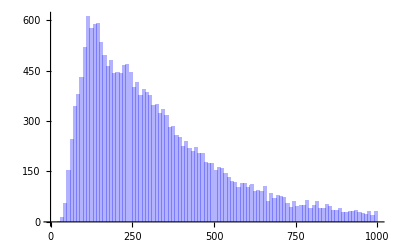

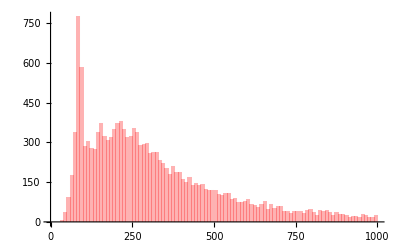

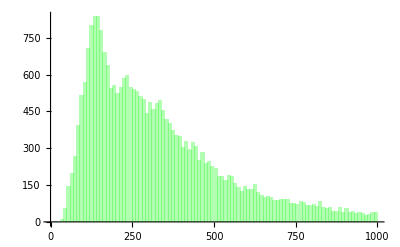

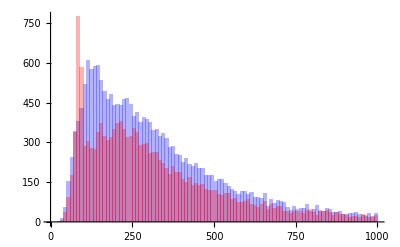

```mathematica
g1=Histogram[AllInvMassPlot, {0,1000,10},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=Histogram[AllInvMassBGPlot, {0,1000,10},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=Histogram[AllInvMassRPVPlot, {0,1000,10},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2]
```

```mathematica
ZDiffList[event_]:={Abs[InvM12[event]-90],Abs[InvM23[event]-90],Abs[InvM34[event]-90],Abs[InvM41[event]-90],Abs[InvM31[event]-90],Abs[InvM24[event]-90],Abs[InvM123[event]-90],Abs[InvM124[event]-90],Abs[InvM423[event]-90],Abs[InvM143[event]-90]}
```

```mathematica
ZFilterInvMass[event_]:=Which[
Min[ZDiffList[event]]==Abs[InvM12[event]-90],InvM12[event],
Min[ZDiffList[event]]==Abs[InvM23[event]-90],InvM23[event],
Min[ZDiffList[event]]==Abs[InvM34[event]-90],InvM34[event],
Min[ZDiffList[event]]==Abs[InvM41[event]-90],InvM41[event],
Min[ZDiffList[event]]==Abs[InvM24[event]-90],InvM24[event],
Min[ZDiffList[event]]==Abs[InvM31[event]-90],InvM31[event],
Min[ZDiffList[event]]==Abs[InvM123[event]-90],InvM123[event],
Min[ZDiffList[event]]==Abs[InvM124[event]-90],InvM124[event],
Min[ZDiffList[event]]==Abs[InvM423[event]-90],InvM423[event],
Min[ZDiffList[event]]==Abs[InvM143[event]-90],InvM143[event]
];
ZFilterInvMassPlot = Flatten[Map[ZFilterInvMass[#] &, eventList4CutJets[[1;;Jet4Nev]]]];
ZFilterInvMassBGPlot = Flatten[Map[ZFilterInvMass[#] &, eventList4CutJets2[[1;;Jet4Nev2]]]];
ZFilterInvMassRPVPlot = Flatten[Map[ZFilterInvMass[#] &, eventList4CutJets3[[1;;Jet4Nev3]]]];
Length[ZFilterInvMassPlot]
```

2071

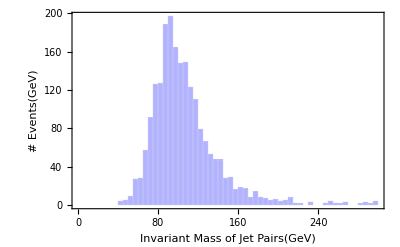

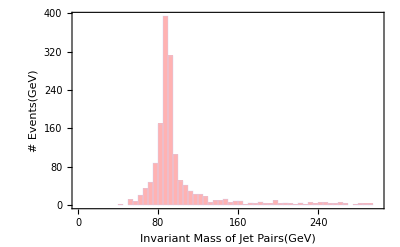

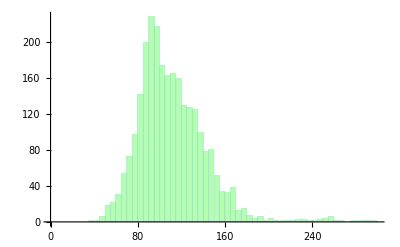

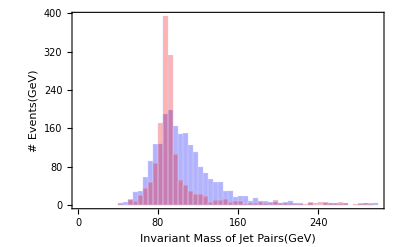

```mathematica
g1=Histogram[ZFilterInvMassPlot, {0,300,5},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"Invariant Mass of Jet Pairs(GeV)","# Events(GeV)"}]
g2=Histogram[ZFilterInvMassBGPlot,{0,300,5},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},AxesOrigin->{0,0},AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"Invariant Mass of Jet Pairs(GeV)","# Events(GeV)"}]
g3=Histogram[ZFilterInvMassRPVPlot,{0,300,5},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2]
```

```mathematica
AllInvMassPairsPlot=Flatten[{Map[InvM12[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM23[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM34[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM41[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM31[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM24[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM51[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM52[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM53[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM54[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM61[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM62[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM63[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM64[#]&,eventList6CutJets[[1;;Jet6Nev]]],Map[InvM65[#]&,eventList6CutJets[[1;;Jet6Nev]]]},1];
AllInvMassPairsBGPlot=Flatten[{Map[InvM12[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM23[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM34[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM41[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM31[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM24[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM51[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM52[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM53[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM54[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM61[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM62[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM63[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM64[#]&,eventList6CutJets2[[1;;Jet6Nev2]]],Map[InvM65[#]&,eventList6CutJets2[[1;;Jet6Nev2]]]},1];
AllInvMassPairsRPVPlot=Flatten[{Map[InvM12[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM23[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM34[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM41[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM31[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM24[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM51[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM52[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM53[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM54[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM61[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM62[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM63[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM64[#]&,eventList6CutJets3[[1;;Jet6Nev3]]],Map[InvM65[#]&,eventList6CutJets3[[1;;Jet6Nev3]]]},1];
```

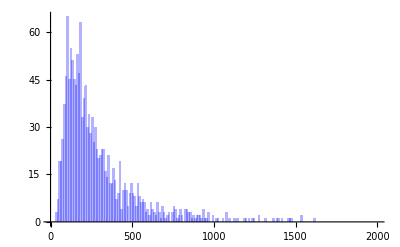

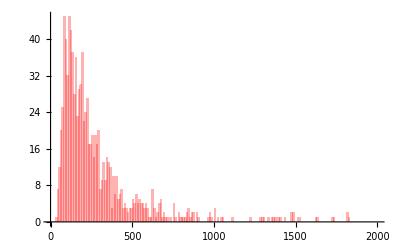

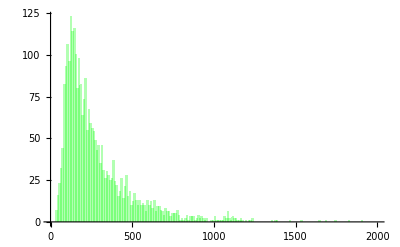

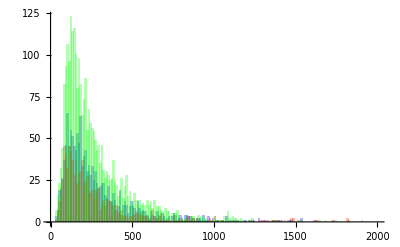

```mathematica
g1=Histogram[AllInvMassPairsPlot, {0,2000,10},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=Histogram[AllInvMassPairsBGPlot, {0,2000,10},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=Histogram[AllInvMassPairsRPVPlot, {0,2000,10},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2,g3]
```

```mathematica
MHT[event_]:=Abs[√((-Total[Map[pxOf,event,{1}]])^2+(-Total[Map[pxOf,event,{1}]])^2)];
```

```mathematica
MHTPlot = Map[MHT[#] &, eventListOutCutJets[[1;;Nev]]];
MHTBGPlot = Map[MHT[#] &, eventListOutCutJets2[[1;;Nev2]]];
MHTLVPlot = Map[MHT[#] &, eventListOutCutJets3[[1;;Nev2]]];
```

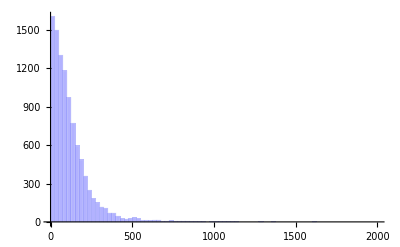

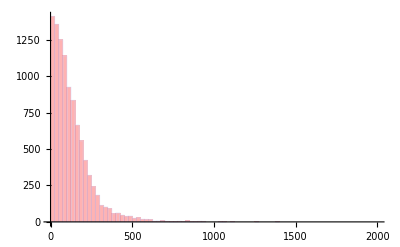

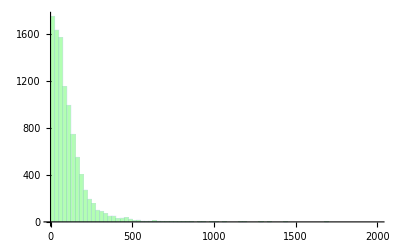

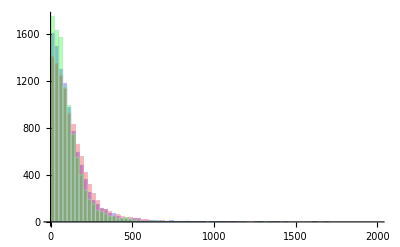

```mathematica
h1=Histogram[MHTPlot, {0,2000,25},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
h2=Histogram[MHTBGPlot, {0,2000,25},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
h4=Histogram[MHTLVPlot, {0,2000,25},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[h1,h2,h4]
```

```mathematica
HtvsMETAxdata=Transpose@{JetPtTotAxPlot,ptmissAxPlot};
HtvsMETGrvdata=Transpose@{JetPtTotGrvPlot,ptmissGrvPlot};
HtvsMETRPVdata=Transpose@{JetPtTotRPVPlot,ptmissRPVPlot};

g1=ListPlot[HtvsMETAxdata]
g2=ListPlot[HtvsMETGrvdata,PlotStyle->Red]
g3 =ListPlot[HtvsMETRPVdata,PlotStyle->Green]
Show[g1,g2,g3]
```

Transpose::nmtx: The first two levels of the one-dimensional list {{1417.59, 650.756, 531.233, 535.412, 314.308, 451.943, 306.197, 418.345, 535.954, 406.474, 1385.68, 216.971, 229.594, 851.144, 508.711, 186.905, 455.415, 260.125, « 16 », 912.253, 318.911, 1319.74, 1725.13, 260.946, 920.539, 563.74, 261.363, 389.323, 377.55, 141.064, 530.944, 299.763, 154.589, 423.253, 1017.3, « 9950 »}, ptmissAxPlot} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {{747.742, 384.124, 261.721, 293.511, 245.476, 579.847, 750.974, 761.071, 294.177, 433.259, 270.605, 222.164, 787.258, 198.772, 338.885, 265.601, 297.025, 955.961, « 16 », 176.526, 234.587, 440.959, 211.629, 380.651, 265.531, 170.944, 1231.61, 347.174, 332.428, 335.843, 523.805, 372.269, 614.358, 416.695, 247.527, « 9950 »}, « 13 »} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {{657.163, 1044.01, 390.858, 534.276, 594.351, 392.098, 245.186, 515.511, 709.484, 769.534, 280.678, 459.611, 397.911, 292.64, 502.862, 181.619, 1738.81, 604.683, « 16 », 748.513, 1744.19, 194.795, 1061.61, 337.238, 849.135, 562.506, 589.642, 675.67, 409.231, 604.078, 151.541, 298.67, 1271.18, 609.394, 920.791, « 9950 »}, « 13 »} cannot be transposed.

ListPlot::lpn: Transpose[{{1417.59, 650.756, 531.233, 535.412, 314.308, 451.943, 306.197, 418.345, 535.954, 406.474, 1385.68, 216.971, 229.594, 851.144, 508.711, 186.905, 455.415, 260.125, « 16 », 912.253, 318.911, 1319.74, 1725.13, 260.946, 920.539, 563.74, 261.363, 389.323, 377.55, 141.064, 530.944, 299.763, 154.589, 423.253, 1017.3, « 9950 »}, « 12 »}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{1417.59,650.756,531.233,535.412,314.308,451.943,306.197,418.345,535.954,406.474,1385.68,216.971,229.594,851.144,508.711,186.905,455.415,«9967»,424.663,287.185,236.479,418.924,352.81,231.369,187.965,478.484,541.906,311.843,449.111,374.191,315.937,383.417,730.208,732.537},ptmissAxPlot}]]

ListPlot::lpn: Transpose[{{747.742, 384.124, 261.721, 293.511, 245.476, 579.847, 750.974, 761.071, 294.177, 433.259, 270.605, 222.164, 787.258, 198.772, 338.885, 265.601, 297.025, « 17 », 176.526, 234.587, 440.959, 211.629, 380.651, 265.531, 170.944, 1231.61, 347.174, 332.428, 335.843, 523.805, 372.269, 614.358, 416.695, 247.527, « 9950 »}, ptmissGrvPlot}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{747.742,384.124,261.721,293.511,245.476,579.847,750.974,761.071,294.177,433.259,270.605,222.164,787.258,198.772,338.885,265.601,297.025,«9967»,450.934,525.37,417.944,1198.67,607.078,258.426,200.573,442.79,1054.74,134.715,626.907,575.154,413.799,176.211,587.033,595.488},ptmissGrvPlot}],«1»]

ListPlot::lpn: Transpose[{{657.163, 1044.01, 390.858, 534.276, 594.351, 392.098, 245.186, 515.511, 709.484, 769.534, 280.678, 459.611, 397.911, 292.64, 502.862, 181.619, 1738.81, « 17 », 748.513, 1744.19, 194.795, 1061.61, 337.238, 849.135, 562.506, 589.642, 675.67, 409.231, 604.078, 151.541, 298.67, 1271.18, 609.394, 920.791, « 9950 »}, ptmissRPVPlot}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{{657.163,1044.01,390.858,534.276,594.351,392.098,245.186,515.511,709.484,769.534,280.678,459.611,397.911,292.64,502.862,181.619,1738.81,«9967»,463.126,989.103,580.531,518.071,395.811,790.032,940.614,271.495,619.233,880.281,516.387,873.593,965.112,282.743,360.885,345.142},ptmissRPVPlot}],«1»]

Show::gcomb: Could not combine the graphics objects in « 1 ».

Show[«1»]